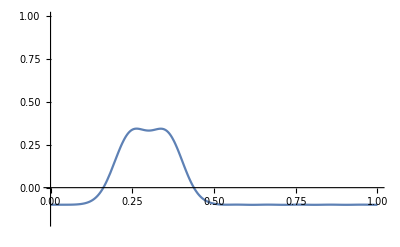

```mathematica
n=20;
l=1;
h=0.005;
g=9.81;
f[x_]:=1/((0.2)2π)Exp[-0.5((x/l-0.3)/0.05)^2];
fVal=NIntegrate[f[x],{x,0,l}];
fNorm[x_]:=f[x]-fVal;
coeff=Table[2/l NIntegrate[f[x]Cos[(i π)/l x],{x,0,l}],{i,1,n}];
omega=Table[√((i π)/l g Tanh[(i π)/l h]),{i,1,n}];
basis=Table[Cos[(i π)/l x]Cos[omega[[i]] time],{i,1,n}];
(*Manipulate[*)
Show[
(*Plot[fNorm[x],{x,0,l},PlotRange->{-1,1},PlotStyle->Red],*)
Plot[basis.coeff/.{time->0.25},{x,0,l},PlotRange->{-0.2,1}]
]
(*,{t,0,4π,AnimationRate->1/50,Appearance->"Open"}]*)
```

```mathematica
Plot3D[basis.coeff,{x,0,l},{time,0,10},PlotRange->Full,MaxRecursion->4]
```

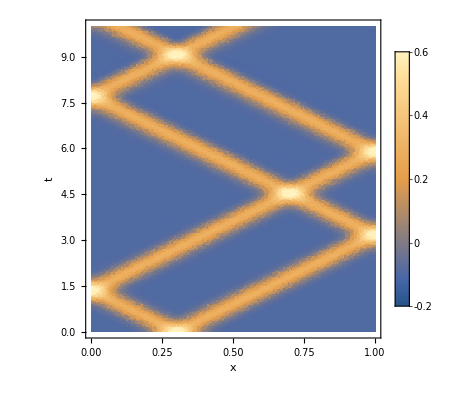

```mathematica
DensityPlot[basis.coeff,{x,0,l},{time,0,10},PlotRange->Full,MaxRecursion->4,FrameLabel->{"x","t"},PlotLegends->BarLegend[{Automatic,{-0.2,0.6}}],ColorFunctionScaling->False,ColorFunction->(ColorData["M10DefaultDensityGradient","ColorFunction"][Rescale[#,{-0.2,0.6}]]&)]
```